## Global Properties

### Packages

```mathematica
Needs["NumericalCalculus`"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor, color,txfonts}"}];
```

### Setup

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor, color, txfonts, amsfonts, amssymb, ulem, amsmath}"},Magnification->1.3];
colors=ColorData[10,"ColorList"];
colorsb=Reverse[ColorData[10, "ColorList"]];
colorsc=ColorData[10, "ColorList"][[5;;]];
tex:=MaTeX;
SetOptions[{Plot,LogPlot,ListLinePlot, ListLogPlot,LogLogPlot,ListPlot,ListLogLinearPlot,ListLogLogPlot,LogLinearPlot,ParametricPlot},
Frame->True, FrameStyle->Black, PlotStyle-> Join[{Black, Blue}, colors, {colors[[1]]}],  ImageSize->350, Background->White, PlotRangePadding->None];
SetDirectory[NotebookDirectory[]];
```

## Plots!

```mathematica
(*IMPORTS*)
Normy = Import["Test_N3F6_Normal.csv"];
Normy = Drop[Normy,1];
LargeN = Import["Test_N3F6_LargeN.csv"];
LargeN = Drop[LargeN,1];
```

```mathematica
(*Include only those points with a PT*)
CroppedNormy= Select[Normy, #[[10]]>0&];
CroppedLargeN = Select[LargeN, #[[10]]>0&];
```

### Normal Case:

#### m_σ^2:

```mathematica
mσ2Contour=Table[{
	CroppedNormy[[j]][[2]]/(CroppedNormy[[j]][[4]])^2,
	CroppedNormy[[j]][[1]]/(CroppedNormy[[j]][[4]])^2,
	1-(CroppedNormy[[j]][[10]]/CroppedNormy[[j]][[9]])},{j,1,Length[CroppedNormy]}];


(*Group rows by first two columns*)
groups=GatherBy[mσ2Contour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxmσ2Contour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];
```

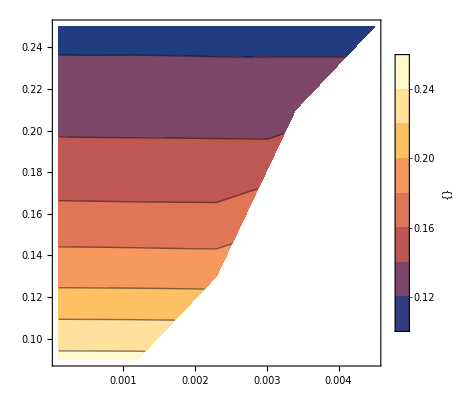

```mathematica
MagPlot=ListContourPlot[maxmσ2Contour,FrameLabel->{MaTeX["M_{\eta'}^2/f_\pi^2", Magnification->1.3], MaTeX["M_{\sigma}^2/f_\pi^2", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["1-T_n/T_c",Magnification->1.3]}]]
```

#### m_X^2:

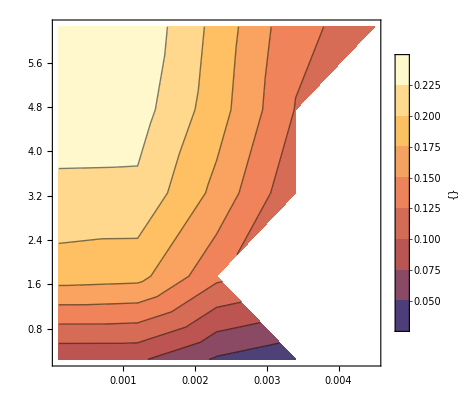

```mathematica
mX2Contour=Table[{
	CroppedNormy[[j]][[2]]/(CroppedNormy[[j]][[4]])^2,
	CroppedNormy[[j]][[3]]/(CroppedNormy[[j]][[4]])^2,
	1-(CroppedNormy[[j]][[10]]/CroppedNormy[[j]][[9]])},{j,1,Length[CroppedNormy]}];


(*Group rows by first two columns*)
groups=GatherBy[mX2Contour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxmX2Contour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlot=ListContourPlot[maxmX2Contour,FrameLabel->{MaTeX["M_{\eta'}^2/f_\pi^2", Magnification->1.3], MaTeX["M_X^2/f_\pi^2", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["1-T_n/T_c",Magnification->1.3]}]]
```

#### m^2:

```mathematica
m2Contour=Table[{
	CroppedNormy[[j]][[2]]/(CroppedNormy[[j]][[4]])^2,
	CroppedNormy[[j]][[5]],
	1-(CroppedNormy[[j]][[10]]/CroppedNormy[[j]][[9]])},{j,1,Length[CroppedNormy]}];


(*Group rows by first two columns*)
groups=GatherBy[m2Contour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxm2Contour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlot=ListContourPlot[maxm2Contour,FrameLabel->{MaTeX["m_{\eta'}^2", Magnification->1.3], MaTeX["m^2", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["\\text{Max\;}1-T_n/T_c",Magnification->1.3]}]]
```

-Graphics-

#### c :

```mathematica
cContour = Table[{
	CroppedNormy[[j]][[2]]/(CroppedNormy[[j]][[4]])^2,
	CroppedNormy[[j]][[6]],
	1-(CroppedNormy[[j]][[10]]/CroppedNormy[[j]][[9]])},{j,1,Length[CroppedNormy]}];

(*Group rows by first two columns*)
groups=GatherBy[cContour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxcContour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlotc=ListContourPlot[maxcContour,FrameLabel->{MaTeX["M_{\eta'}^2/f_\pi^2", Magnification->1.3], MaTeX["c", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["1-T_n/T_c",Magnification->1.3]}]]
```

-Graphics-

#### λ_σ:

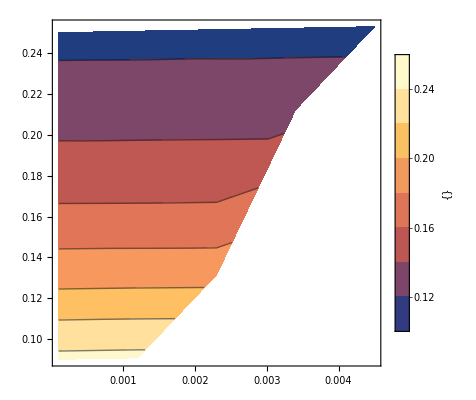

```mathematica
λσContour = Table[{
	CroppedNormy[[j]][[2]]/(CroppedNormy[[j]][[4]])^2,
	CroppedNormy[[j]][[7]],
	1-(CroppedNormy[[j]][[10]]/CroppedNormy[[j]][[9]])},{j,1,Length[CroppedNormy]}];

(*Group rows by first two columns*)
groups=GatherBy[λσContour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxλσContour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlot=ListContourPlot[maxλσContour,FrameLabel->{MaTeX["M_{\eta'}^2/f_\pi^2", Magnification->1.3], MaTeX["\lambda_\sigma", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["1-T_n/T_c",Magnification->1.3]}]]
```

#### λ_a:

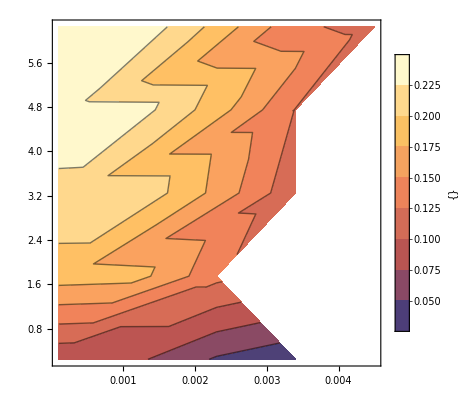

```mathematica
λaContour=Table[{
	CroppedNormy[[j]][[2]]/(CroppedNormy[[j]][[4]])^2,
	CroppedNormy[[j]][[8]],
	1-(CroppedNormy[[j]][[10]]/CroppedNormy[[j]][[9]])},{j,1,Length[CroppedNormy]}];


(*Group rows by first two columns*)
groups=GatherBy[λaContour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxλaContour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlot=ListContourPlot[maxλaContour,FrameLabel->{MaTeX["M_{\eta'}^2/f_\pi^2", Magnification->1.3], MaTeX["\lambda_a", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["1-T_n/T_c",Magnification->1.3]}]]
```

### Large N Case :

#### m_σ^2:

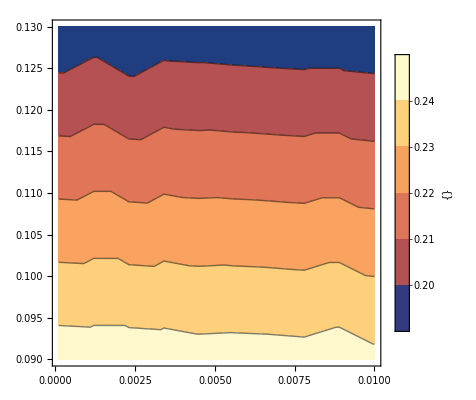

```mathematica
mσ2Contour=Table[{
	CroppedLargeN[[j]][[2]]/(CroppedLargeN[[j]][[4]])^2,
	CroppedLargeN[[j]][[1]]/(CroppedLargeN[[j]][[4]])^2,
	1-(CroppedLargeN[[j]][[10]]/CroppedLargeN[[j]][[9]])},{j,1,Length[CroppedLargeN]}];


(*Group rows by first two columns*)
groups=GatherBy[mσ2Contour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxmσ2Contour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlot=ListContourPlot[maxmσ2Contour,FrameLabel->{MaTeX["M_{\eta'}^2/f_\pi^2", Magnification->1.3], MaTeX["M_{\sigma}^2/f_\pi^2", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["1-T_n/T_c",Magnification->1.3]}]]
```

#### m_X^2:

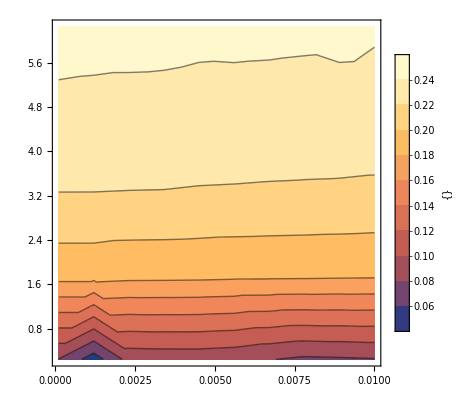

```mathematica
mX2Contour=Table[{
	CroppedLargeN[[j]][[2]]/(CroppedLargeN[[j]][[4]])^2,
	CroppedLargeN[[j]][[3]]/(CroppedLargeN[[j]][[4]])^2,
	1-(CroppedLargeN[[j]][[10]]/CroppedLargeN[[j]][[9]])},{j,1,Length[CroppedLargeN]}];


(*Group rows by first two columns*)
groups=GatherBy[mX2Contour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxmX2Contour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlot=ListContourPlot[maxmX2Contour,FrameLabel->{MaTeX["M_{\eta'}^2/f_\pi^2", Magnification->1.3], MaTeX["M_X^2/f_\pi^2", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["1-T_n/T_c",Magnification->1.3]}]]
```

#### m^2:

```mathematica
m2Contour=Table[{
	CroppedLargeN[[j]][[2]]/(CroppedLargeN[[j]][[4]])^2,
	CroppedLargeN[[j]][[5]],
	1-(CroppedLargeN[[j]][[10]]/CroppedLargeN[[j]][[9]])},{j,1,Length[CroppedLargeN]}];


(*Group rows by first two columns*)
groups=GatherBy[m2Contour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxm2Contour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlot=ListContourPlot[maxm2Contour,FrameLabel->{MaTeX["m_{\eta'}^2", Magnification->1.3], MaTeX["m^2", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["\\text{Max\;}1-T_n/T_c",Magnification->1.3]}]]
```

-Graphics-

#### c :

```mathematica
cContour = Table[{
	CroppedLargeN[[j]][[2]]/(CroppedLargeN[[j]][[4]])^2,
	CroppedLargeN[[j]][[6]],
	1-(CroppedLargeN[[j]][[10]]/CroppedLargeN[[j]][[9]])},{j,1,Length[CroppedLargeN]}];

(*Group rows by first two columns*)
groups=GatherBy[cContour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxcContour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlotc=ListContourPlot[maxcContour,FrameLabel->{MaTeX["M_{\eta'}^2/f_\pi^2", Magnification->1.3], MaTeX["c", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["1-T_n/T_c",Magnification->1.3]}]]
```

-Graphics-

#### λ_σ:

```mathematica
λσContour = Table[{
	CroppedLargeN[[j]][[2]]/(CroppedLargeN[[j]][[4]])^2,
	CroppedLargeN[[j]][[7]],
	1-(CroppedLargeN[[j]][[10]]/CroppedLargeN[[j]][[9]])},{j,1,Length[CroppedLargeN]}];

(*Group rows by first two columns*)
groups=GatherBy[λσContour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxλσContour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlot=ListContourPlot[maxλσContour,FrameLabel->{MaTeX["M_{\eta'}^2/f_\pi^2", Magnification->1.3], MaTeX["\lambda_\sigma", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["1-T_n/T_c",Magnification->1.3]}]]
```

-Graphics-

#### λ_a:

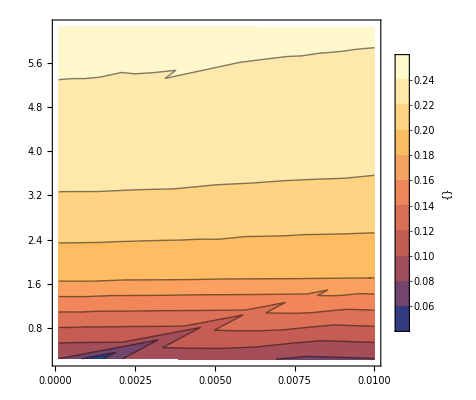

```mathematica
λaContour=Table[{
	CroppedLargeN[[j]][[2]]/(CroppedLargeN[[j]][[4]])^2,
	CroppedLargeN[[j]][[8]],
	1-(CroppedLargeN[[j]][[10]]/CroppedLargeN[[j]][[9]])},{j,1,Length[CroppedLargeN]}];


(*Group rows by first two columns*)
groups=GatherBy[λaContour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxλaContour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];

MagPlot=ListContourPlot[maxλaContour,FrameLabel->{MaTeX["M_{\eta'}^2/f_\pi^2", Magnification->1.3], MaTeX["\lambda_a", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["1-T_n/T_c",Magnification->1.3]}]]
```